# Monroe Optimization 2.0 Last Updated: 3/19/2021

```mathematica
Remove["Global`*"]
```

## 1 Get eigen

## 1.1 Setup

```mathematica
SetAttributes[{m0,m1,kz},Constant];
m={m0,m0,m0,m0,m1};(*Enter chain configuration here: 1 is lower mass ion, a is higher mass ion*)
wmhz=2*Pi*1*^6;Num =Length[m];
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];
xM = Array[x,{3,Num}];
	(*Calculate equilibrium positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist =L0EQ/@Range[Num]//FullSimplify;
guessz0=Range[-#,#,2*#/(Num-1)]&[0.7*Num^(2/3)];pos=Transpose[Append[{z0M},guessz0]];z0M=z0M/.Chop[FindRoot[L0EQlist,pos]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
	(*Create matrix*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{Num*(Num+3)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
Vel1norm=Vel1/.{m1->m0,k[1,2]->k[1,1],k[2,2]->k[2,1]}//FullSimplify;
	(*Subbing in secular frequency expressions*)
{k[1,1],k[1,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
{k[2,1],k[2,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(-κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
kz=3.204*^-13*κz*U/z0^2//FullSimplify;
αred=V0^2/w^2/U*(z0/r0^2)^2;
```

```mathematica
(*sub in values*)
V1=0;
```

## 1.2 Get normal modes

```mathematica
Clear[V0,U,w,r0,z0];
(*Enter mass values here: m0 is mass of lighter ion, m1hold is mass of heavier ion (>1),*)
m1hold=171*1.66054*^-27;m0=138*1.66054*^-27;κr=1;κz=1;r0=0.2;z0=0.4;
eigenholder=Table[Eigensystem[Vel1[[d]]/.{m1->m1hold}],{d,3}];
wmlist=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlist=eigenholder[[;;,2]]//FullSimplify;

eigenholder=Table[Eigensystem[Vel1[[d]]/.{m1->m0}],{d,3}];
wmlistnorm=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlistnorm=Chop[eigenholder[[;;,2]]/.{V0->1,U->1,w->1}//FullSimplify];
m1=m1hold;
```

## 1.2 Get normal modes

```mathematica
uholder=NSolve[Sqrt[kz/m1]==0.16*wmhz,U];vholder=NSolve[Sqrt[k[1,2]/m1]==3.06*wmhz/.uholder/.w->28.3,V0];
solnsMONROE={vholder[[1,1]],uholder[[1,1]],w->28.3}

wmlist[[1]]/.solnsMONROE/.{w->28.3}
wmlist[[3]]/.solnsMONROE/.{w->28.3}
```

{V0→343.043,U→0.143309,w→28.3}

{3.79109,3.78443,3.7758,3.76626,3.05345}

{0.653171,0.539854,0.418094,0.294484,0.173734}

## 2 Optimizing parameters

## 2.1 Constraints & prep

```mathematica
qmax=0.4;tempK=0.1;constrmax = 1*^40;V1max=0;Umax=1000;
zigzag=AllTrue[wmlist[[1]],Im[#]==0&]//FullSimplify;
resids=Total[(vlist[[1,;;,1;;(Num-1)]]-vlistnorm[[1,;;,1;;(Num-1)]])^2,2];
trapConstr={100≤V0≤400,0<U<(6.696294*^-28*(V0/w/r0)^2/m1-0.33*V1)*(z0/r0)^2,10≤w≤40};
kConstr={k[1,2]>kz,k[2,2]>kz,8.11582681*^-27/m0/qmax*V0<(r0*w)^2}//FullSimplify;
wConstr=FullSimplify[3.25*^-40/m1^2*κr^2*V0^2/w^2/r0^4+1.602*^-13*(-κz*U/z0^2)/m1]>(1*wmhz)^2;
```

## 2.2 Optimization functions

```mathematica
(*only optimize α-*)
αredfunct[V0s_,Us_,ws_]:=If[zigzag/.#,αred/.#,constrmax]&[{V0->V0s,U->Us,w->ws}];
solnsαRED=NMinimize[{αredfunct[V0,U,w],kConstr[[3]],trapConstr},{V0,U,w},MaxIterations->1000][[2]];
{MatrixForm[#],MatrixForm[vlist[[1]]/.#],MatrixForm[wmlist[[1]]/.#],MatrixForm[Append[kConstr,wConstr]/.#]}&[solnsαRED]
```

{(V0→300.709
U→3.72414
w→39.8808),(3.52522 | 3.20054 | 2.81692 | 2.25533 | 1.
-1.91546 | -0.163934 | 0.977421 | 1.56242 | 1.
0.587821 | -0.724483 | -0.543252 | 0.344445 | 1.
-0.347447 | 0.848799 | -0.205179 | -0.848574 | 1.
0.614133 | -2.78206 | 4.36899 | -2.91219 | 1.),(2.2356
1.95974
1.57854
1.20836
0.0000719058),(True
True
True
True)}

```mathematica
(*Optimize for least squares*)
vlsqx[V0s_,Us_,ws_]:=If[zigzag/.#,resids/.#,constrmax]&[{V0->V0s,U->Us,w->ws}];
solnsLSQ=NMinimize[{vlsqx[V0,U,w],kConstr[[3]],trapConstr},{V0,U,w},MaxIterations->1000][[2]];
{MatrixForm[#],MatrixForm[vlist[[1]]/.#],MatrixForm[wmlist[[1]]/.#],MatrixForm[Append[kConstr,wConstr]/.#]}&[solnsLSQ]
```

{(V0→100.103
V1→0.
U→8.72919
w→39.9325),(2.63894 | 1.
-0.530516 | 1.),(0.236427
0.0872046),(True
True
True),False}

```mathematica
(*get max and min U*)
specConstr={100≤V0≤2000,0<U<(6.696294*^-28*(V0/w/r0)^2/m1)*(z0/r0)^2};
αredfunct[V0s_,V1s_,Us_,ws_]:=If[zigzag/.{V0->V0s,U->Us,w->40},αred/.{V0->V0s,U->Us,w->40},constrmax];
solnsα1RED=NMinimize[{αredfunct[V0,V1,U,w],kConstr[[3]],Append[specConstr,40≤w≤40]},{V0,V1,U,w},MaxIterations->1000][[2]];
{MatrixForm[#],MatrixForm[vlist[[1]]/.#],MatrixForm[wmlist[[1]]/.#],MatrixForm[{k[1,1],k[1,2]}/.#],MatrixForm[kConstr/.#]}&[solnsα1RED]

αredfunct[V0s_,V1s_,Us_,ws_]:=If[zigzag/.{V0->V0s,V1->0,U->Us,w->14.8835},αred/.{V0->V0s,U->Us,w->14.8835},constrmax];
solnsα2RED=NMinimize[{αredfunct[V0,V1,U,w],kConstr[[3]],Append[specConstr,14.8835≤w≤14.8835]},{V0,V1,U,w},MaxIterations->1000][[2]];
{MatrixForm[#],MatrixForm[vlist[[1]]/.#],MatrixForm[wmlist[[1]]/.#],MatrixForm[{k[1,1],k[1,2]}/.#],MatrixForm[kConstr/.#]}&[solnsα2RED]
```

{(V0→100.023
V1→0.
U→8.68582
w→40.),(2.63894 | 1.
-0.530516 | 1.),(0.235839
0.0869877),(1.80415×10^-13
1.12965×10^-13),(True
True
True)}

{(V0→100.
V1→0.
U→62.7079
w→14.8835),(2.63894 | 1.
-0.530516 | 1.),(0.633681
0.23373),(1.30252×10^-12
8.15561×10^-13),(True
True
True)}

## 2.4 Print solutions

```mathematica
(*Print solutions*)
solnsDJ=solnsMONROE; (*Enter which solution you want formatted: solnsLSQ for least squares, solnsQRMS for root mean square position*)
		(*trap/ion parameters*)
eigenholder2=Table[Eigensystem[Vel1[[d]]/.solnsDJ],{d,3}];wmvals=Sqrt[-eigenholder2[[;;,1]]]/wmhz//FullSimplify;
vvals=Table[Normalize[eigenholder2[[d,2,i]]],{d,3},{i,Num}]//FullSimplify;
vlistnorm=Table[Normalize[vlistnorm[[d,i]]],{d,3},{i,Num}]//FullSimplify;
wsecvals=Sqrt[{{k[1,1],k[1,2]}/{m0,m1},{k[2,1],k[2,2]}/{m0,m1},kz/{m0,m1}}]/wmhz/.solnsDJ;
qx=8.11582681*^-27*V0/w^2/r0^2/{m0,m1}/.solnsDJ;
		(*rms position fluctuation*)
gim=Table[Transpose[vvals[[d]]],{d,3}];fwm=1/wmvals[[1]]/wmhz*(1/(Exp[wmvals[[1]]*4.8*^-5/tempK]-1)+0.5);
rmsq2=Sqrt[(gim[[1]]^2).fwm*5.2728*^-35/m];
		(*format 1*)
res1=Table[{MatrixForm[vvals[[d,j]]],wmvals[[d,j]]},{d,3},{j,Num}];
normres1=Table[{MatrixForm[Normalize[vlistnorm[[1,i]]]],wmlistnorm[[1,i]]}/.solnsDJ,{i,Num}];
res2=Transpose[{wsecvals[[1,;;2]],wsecvals[[2,;;2]],wsecvals[[3,;;2]],qx[[;;2]]}];
		(*format 2*)
MatrixForm[solnsDJ]
TableForm[{{TableForm[res1[[1]],TableHeadings->{None,{"Eigenvector", "Mode Freq.(x2π MHz)"}}],TableForm[normres1,TableHeadings->{None,{"Eigenvector", "Mode Freq.(x2π MHz)"}}]}},TableHeadings->{None,{"Mixed-Species","Single-Species"}}]
TableForm[res2,TableHeadings->{{"Atom","Molecule"},{"x-ω_sec(x2π MHz)", "y-ω_sec(x2π MHz)","z-ω_sec(x2π MHz)", "q_x-parameter"}}]
TableForm[Transpose[{rmsq2}],TableHeadings->{Table[TextString[m[[i]]/m0],{i,Num}],{"√(<q^2>)@0.1K"}}]
```

(V0→343.043
U→0.143309
w→28.3)

Mixed-Species | Single-Species
Eigenvector | Mode Freq.(x2π MHz)
(-0.629683
-0.54715
-0.451843
-0.316156
-0.00303444) | 3.79109
(0.680016
-0.0707486
-0.473303
-0.555461
-0.00449858) | 3.78443
(-0.358916
0.674599
0.125965
-0.63262
-0.00436166) | 3.7758
(-0.110708
0.490446
-0.745623
0.437317
0.00261325) | 3.76626
(-0.000127795
-0.000317857
-0.0010024
-0.00736044
0.999972) | 3.05345 | Eigenvector | Mode Freq.(x2π MHz)
(0.446595
0.443878
0.440504
0.435267
0.469068) | 3.79109
(-0.613291
-0.312096
-0.0360101
0.251564
0.679625) | 3.78443
(0.559865
-0.239356
-0.512621
-0.346505
0.496401) | 3.7758
(-0.315805
0.649815
0.031063
-0.642692
0.252964) | 3.76626
(0.10605
-0.475415
0.735469
-0.462753
0.0876379) | 3.05345

| x-ω_sec(x2π MHz) | y-ω_sec(x2π MHz) | z-ω_sec(x2π MHz) | q_x-parameter
Atom | 3.79224 | 3.79224 | 0.178106 | 0.379245
Molecule | 3.06 | 3.06 | 0.16 | 0.306057

| √(<q^2>)@0.1K
1.0 | 7.2962×10^-8
1.0 | 7.31094×10^-8
1.0 | 7.31595×10^-8
1.0 | 7.31095×10^-8
1.23913 | 8.12628×10^-8

## 3 Plotting

## 3.1 Plot for eigenvector ratios - U

2.63082

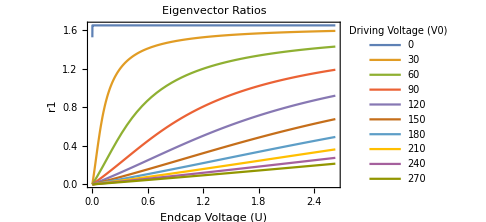
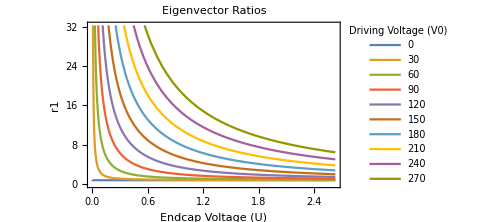
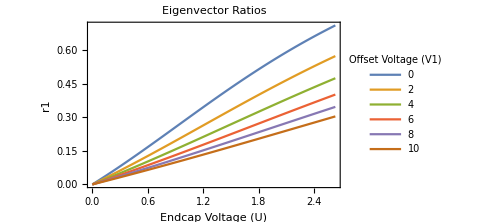
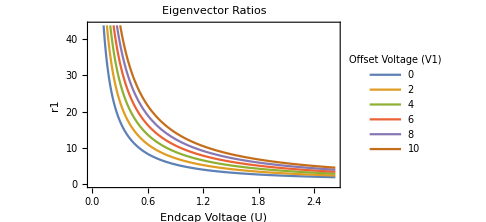
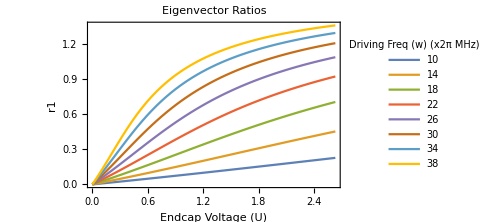
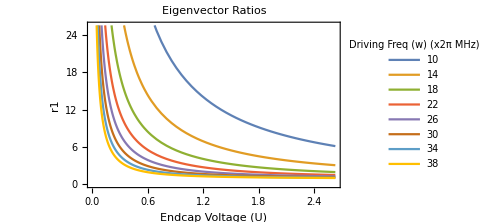

```mathematica
{V0,V1,U,w,r0,z0}={V0,V1,U,w,r0,z0}/.solnsDJ;(*uses same parameters as those from 1.2.3*)
V0range=150;V0step=30;V1range=10;V1step=2;wmin=10;wmax=40;wstep=4;
(*Enter range and step for V0, V1, and w (w is in units of 2pi MHz)*)
xmin=0;xmax=(4.059*^-27*(V0/w)^2/m0+V1)*2/3

{Table[Plot[Evaluate@Table[Abs[vRatx[x1,V1,x2,w,r0,z0][[i,j]]]//FullSimplify,{x1,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step},{j,Num-1}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[di,Num-1],{di,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step}]],LegendLabel->"Driving Voltage (V0)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}],Table[Plot[Evaluate@Table[Abs[vRatx[V0,x1,x2,w,r0,z0][[i,j]]]//FullSimplify,{x1,If[V1≤V1range,0,V1-V1range],V1max,V1step},{j,Num-1}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[di,Num-1],{di,If[V1≤V1range,0,V1-V1range],V1max,V1step}]],LegendLabel->"Offset Voltage (V1)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}],
Table[Plot[Evaluate@Table[Abs[vRatx[V0,V1,x2,x1,r0,z0][[i,j]]]//FullSimplify,{x1,wmin,wmax,wstep},{j,Num-1}],{x2,xmin,xmax}, PlotLegends->LineLegend[Flatten[Table[ConstantArray[di,Num-1],{di,wmin,wmax,wstep}]],LegendLabel->"Driving Freq (w) (x2π MHz)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}]}

Clear[V0,V1,U,w,r0,z0]
```

## 3.2 Plot for eigenvector ratios - V1

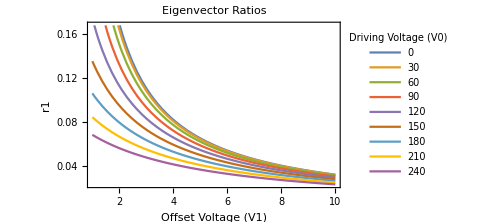
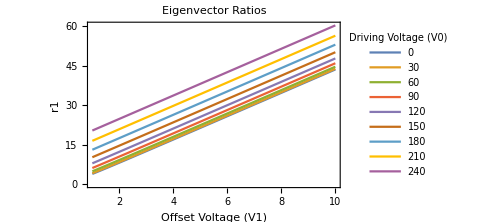
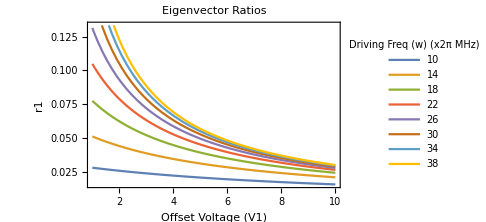
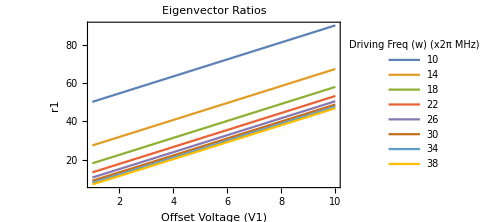
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
{V0,V1,U,w,r0,z0}={V0,V1,U,w,r0,z0}/.solnsDJ;
V0range=150;V0step=30;wmin=10;wmax=40;wstep=4;Umin=0;Umax=(4.059*^-27*(V0/w)^2/m0+V1)*2/3;Ustep=0.5;
(*Enter range and step for V0, U, and w (w is in units of 2pi MHz)*)
xmin=0;xmax=V1max;

{Table[Plot[Evaluate@Table[Abs[vRatx[x1,x2,U,w,r0,z0][[i,j]]]//FullSimplify,{x1,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step},{j,Num-1}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step}]],LegendLabel->"Driving Voltage (V0)"],Frame->True,FrameLabel->{"Offset Voltage (V1)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}],Table[Plot[Evaluate@Table[Abs[vRatx[V0,x2,x1,w,r0,z0][[i,j]]]//FullSimplify,{x1,Umin,Umax,Ustep},{j,Num-1}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,Umin,Umax,Ustep}]],LegendLabel->"Endcap Voltage (U)"],Frame->True,FrameLabel->{"Offset Voltage (V1)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}],
Table[Plot[Evaluate@Table[Abs[vRatx[V0,x2,U,x1,r0,z0][[i,j]]]//FullSimplify,{x1,wmin,wmax,wstep},{j,Num-1}],{x2,xmin,xmax}, PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,wmin,wmax,wstep}]],LegendLabel->"Driving Freq (w) (x2π MHz)"],Frame->True,FrameLabel->{"Offset Voltage (V1)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],{i,Num}]}

Clear[V0,V1,U,w,r0,z0]
```

## 3.3 Plot ratios for position fluctuation - U

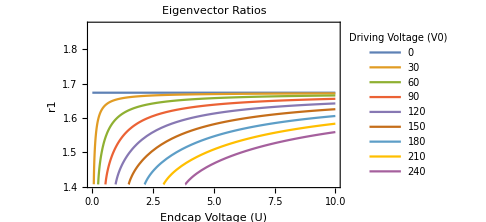
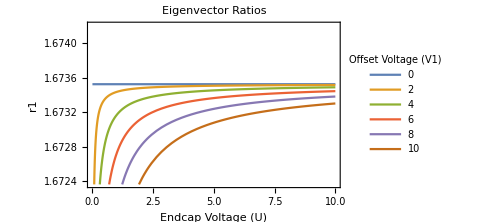
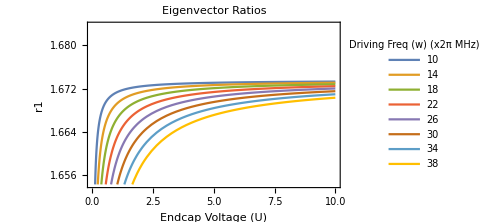

```mathematica
{V0,V1,U,w,r0,z0}={V0,V1,U,w,r0,z0}/.solnsDJ;
V0range=150;V0step=30;wmin=10;wmax=40;wstep=4;Umin=0;Umax=(4.059*^-27*(V0/w)^2/m0+V1)*2/3;Ustep=1;
(*Enter range and step for V0, U, and w (w is in units of 2pi MHz)*)
xmin=0;xmax=V1max;

{Plot[Evaluate@Table[qrmsRatx[x1,V1,x2,w,r0,z0]//FullSimplify,{x1,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,If[V0≤V0range,0,V0-V0range],V0+V0range,V0step}]],LegendLabel->"Driving Voltage (V0)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],Plot[Evaluate@Table[qrmsRatx[x1,V1,x2,w,r0,z0]//FullSimplify,{x1,If[V1≤V1range,0,V1-V1range],V1max,V1step}],{x2,xmin,xmax},PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,If[V1≤V1range,0,V1-V1range],V1max,V1step}]],LegendLabel->"Offset Voltage (V1)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium],
Plot[Evaluate@Table[qrmsRatx[x1,V1,x2,w,r0,z0]//FullSimplify,{x1,wmin,wmax,wstep}],{x2,xmin,xmax}, PlotLegends->LineLegend[Flatten[Table[ConstantArray[i,Num-1],{i,wmin,wmax,wstep}]],LegendLabel->"Driving Freq (w) (x2π MHz)"],Frame->True,FrameLabel->{"Endcap Voltage (U)","r1"},PlotLabel->Style["Eigenvector Ratios"],ImageSize->Medium]}

Clear[V0,V1,U,w,r0,z0]
```

## 4 Pretty Pictures

```mathematica
monxplot=Table[BarChart[vvals[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
monzplot=Table[BarChart[vvals[[3,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[3,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
```

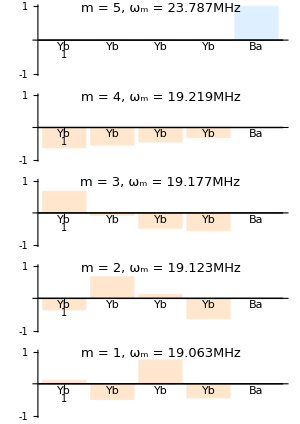
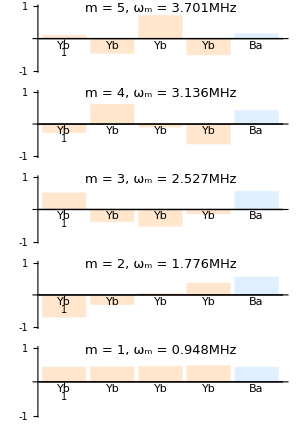

```mathematica
{GraphicsColumn[monxplot,Frame->All,ImageSize->300],GraphicsColumn[monzplot,Frame->All,ImageSize->300]}
```

```mathematica
lsqxplot=Table[BarChart[vvals[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
lsqzplot=Table[BarChart[vvals[[3,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
```

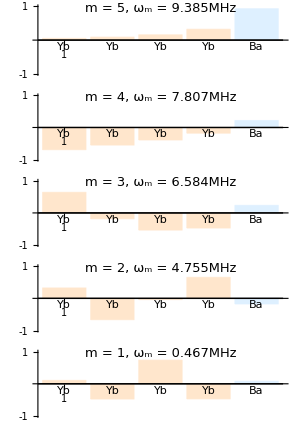
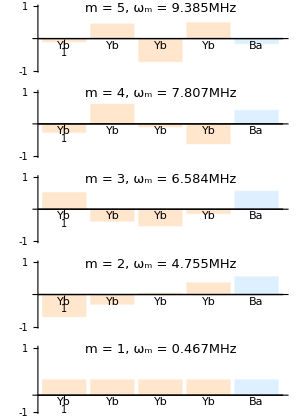

```mathematica
{GraphicsColumn[lsqxplot,Frame->All,ImageSize->300],GraphicsColumn[lsqzplot,Frame->All,ImageSize->300]}
```

```mathematica
vthde=Chop[Table[Normalize[vlistnorm[[d,i]]]/.solnsLSQ,{d,3},{i,Num}]];
wthde=wmlistnorm/.solnsLSQ;
nx=Table[BarChart[vthde[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightOrange},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wthde[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
nz=Table[BarChart[vthde[[3,i]],PlotRange->{-1,1},Ticks->{{-1,0,1}},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightOrange},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wthde[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.9}]]],{i,Num}];
```

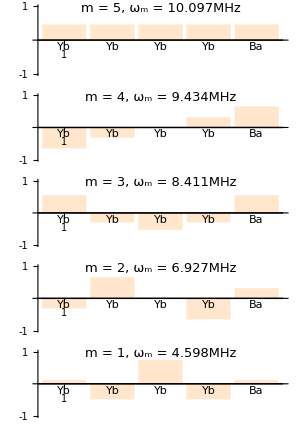
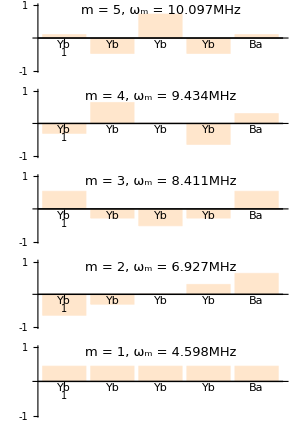

```mathematica
{GraphicsColumn[nx,Frame->All,ImageSize->300],GraphicsColumn[nz,Frame->All,ImageSize->300]}
```